## Unconstrained fitting (Free)

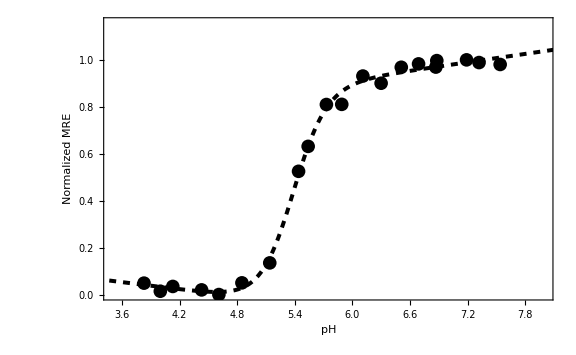

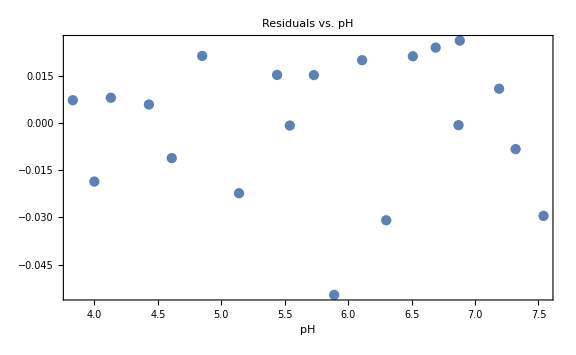

| Estimate | Standard Error | t-Statistic | P-Value
fa | 0.237237 | 0.163064 | 1.45487 | 0.167759
Sa | -0.0511898 | 0.038743 | -1.32127 | 0.2076
fb | 0.561013 | 0.134721 | 4.16426 | 0.000954674
Sb | 0.059529 | 0.0196339 | 3.03195 | 0.00896513
m | 2.51832 | 0.298656 | 8.43217 | 7.38388×10^-7
pKa | 5.37371 | 0.02719 | 197.635 | 1.58818×10^-25

```mathematica
(*Import the data in format {pH,θ}. Use Insert>File Path*)
importfile="/Users/Justin/Documents/Data/CD/pH titration/Roxy-HR/2016-10-28/2016-10-28 R7HR titration.xlsx";

(*Import[importfile,{"Data",sheetnumber,rownumber,columnnumber}]*)
MRE=Import[importfile,{"Data",1,3,Range[209,228]}];pHvalues=Import[importfile,{"Data",1,7,Range[209,228]}];
data=Thread[{pHvalues,MRE}];
normMRE=(MRE-Min[MRE])/(Max[MRE]-Min[MRE]);
normdata=Thread[{pHvalues,normMRE}];
constraint={Sa->0,Sb->0};
Clear[pH]

(*Function to fit the data, remove ";" to see formatted function*)
model=((fa+Sa*pH)+(fb+Sb*pH)*10^(m*(pH-pKa)))/(1+10^(m*(pH-pKa)));

(*Fitting the data. Note: the number after the comma is the 'best first guess' and can be changed*)nlmU1=NonlinearModelFit[normdata,{ model}, {{fa,0},{ Sa,0},{fb,1},{Sb,0},{m,1},{pKa,5.5}},pH];

(*plot the data and the fit*)
Show[{
ListPlot[normdata,PlotStyle->{Black},PlotMarkers->{Automatic,14}],
Plot[nlmU1[pH],{pH,0,10},PlotStyle->{Black,Dashed,Thickness[0.005]}]},
Frame->True,
FrameLabel->{"pH","Normalized MRE"},
FrameStyle->Black,
LabelStyle->{FontSize->25,FontColor->Black},
ImageSize->Large,
TicksStyle->FontSize->25,
PlotRange->{{3.5,8},All}]

(*Plot residuals*)
ListPlot[
Transpose[
{data[[All,1]],
nlmU1["FitResiduals"]}],
Frame->True,
PlotRange->All,
PlotLabel->"Residuals vs. pH",
AxesLabel->{"pH"}]

(*Display best fit parameters*)
nlmU1["ParameterTable"]
```

## Constrained (fixed)

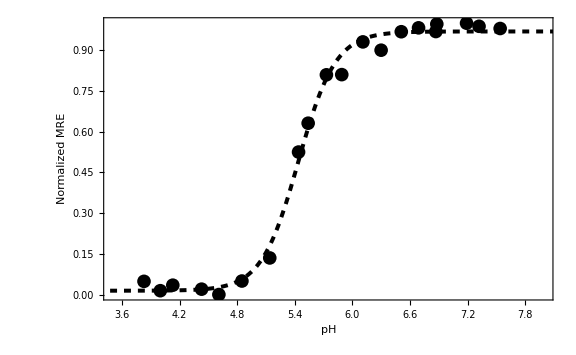

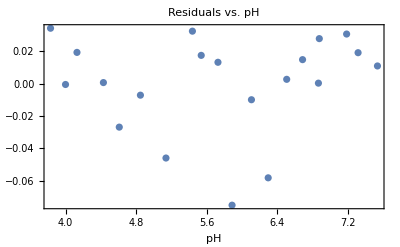

| Estimate | Standard Error | t-Statistic | P-Value
fa | 0.014152 | 0.0159538 | 0.887057 | 0.390033
Sa | 0. | 3.07952×10^-17 | 0. | 1.
fb | 0.969448 | 0.0123749 | 78.3397 | 6.63412×10^-20
Sb | 0. | 0. | ComplexInfinity | 0.
m | 2.25492 | 0.233202 | 9.66938 | 1.41439×10^-7
pKa | 5.43929 | 0.02111 | 257.664 | 3.87858×10^-27

```mathematica
(*Note you may have to change the variable names if you want to evaluate this one first*)
importfile="/Users/Justin/Documents/Data/CD/pH titration/Roxy-HR/2016-10-28/2016-10-28 R7HR titration.xlsx";
MRE=Import[importfile,{"Data",1,3,Range[209,228]}];pHvalues=Import[importfile,{"Data",1,7,Range[209,228]}];
data=Thread[{pHvalues,MRE}];
normMRE=(MRE-Min[MRE])/(Max[MRE]-Min[MRE]);
normdata=Thread[{pHvalues,normMRE}];
constraint={Sa->0,Sb->0};
Clear[pH]

(*Function to fit the data, remove ";" to see formatted function*)
model=((fa+Sa*pH)+(fb+Sb*pH)*10^(m*(pH-pKa)))/(1+10^(m*(pH-pKa)));


(*Fitting the data. Note: the number after the comma is the 'best first guess' and can be changed*)nlmU1=NonlinearModelFit[normdata,{ model/.constraint}, {{fa,0},{ Sa,0},{fb,1},{Sb,0},{m,1},{pKa,5.5}},pH];

(*plot the data and the fit*)
Show[{
ListPlot[normdata,PlotStyle->{Black},PlotMarkers->{Automatic,14}],
Plot[nlmU1[pH],{pH,0,10},PlotStyle->{Black,Dashed,Thickness[0.005]}]},
Frame->True,
FrameLabel->{"pH","Normalized MRE"},
FrameStyle->Black,
LabelStyle->{FontSize->25,FontColor->Black},
ImageSize->Large,
TicksStyle->FontSize->25,
PlotRange->{{3.5,8},All}]

(*Plot residuals*)
ListPlot[
Transpose[
{data[[All,1]],
nlmU1["FitResiduals"]}],
Frame->True,
PlotRange->All,
PlotLabel->"Residuals vs. pH",
AxesLabel->{"pH"}]

(*Display best fit parameters*)
nlmU1["ParameterTable"]
```